```mathematica
data = ReadList["D:\\HOMEWORK\\FOR_HOMEWORK_2020\\20SP\\VE401\\P2\\data-police-shootings\\q2.csv", {Record, Record}, RecordSeparators->{"\n", ","}];
```

```mathematica
Length[data]
```

4938

```mathematica
dates= Map[DateObject, data[[1;;4938, 2]]]
```

{Day: Fri 2 Jan 2015,Day: Fri 2 Jan 2015,Day: Sat 3 Jan 2015,Day: Sun 4 Jan 2015,Day: Sun 4 Jan 2015,Day: Sun 4 Jan 2015,Day: Mon 5 Jan 2015,Day: Tue 6 Jan 2015,Day: Tue 6 Jan 2015,Day: Tue 6 Jan 2015,Day: Tue 6 Jan 2015,Day: Wed 7 Jan 2015,Day: Wed 7 Jan 2015,Day: Wed 7 Jan 2015,Day: Wed 7 Jan 2015,4908,Day: Sun 29 Dec 2019,Day: Sun 29 Dec 2019,Day: Sun 29 Dec 2019,Day: Sun 29 Dec 2019,Day: Sun 29 Dec 2019,Day: Mon 30 Dec 2019,Day: Mon 30 Dec 2019,Day: Mon 30 Dec 2019,Day: Tue 31 Dec 2019,Day: Tue 31 Dec 2019,Day: Tue 31 Dec 2019,Day: Tue 31 Dec 2019,Day: Tue 31 Dec 2019,Day: Tue 31 Dec 2019,Day: Tue 31 Dec 2019}
 |  |  |  |

```mathematica
Commonest[dates]
```

{Day: Sat 6 Jan 2018,Day: Thu 1 Feb 2018,Day: Sun 1 Apr 2018,Day: Fri 29 Jun 2018,Day: Mon 28 Jan 2019}

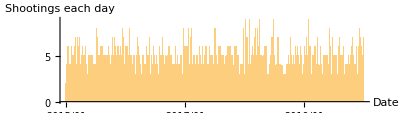

Thread::tdlen: Objects of unequal length in {1957,612} {0.24} cannot be combined.

Set::shape: Lists {System`ConvertersDump`width$249119,System`ConvertersDump`height$249119} and {0.24} {1957,612} are not the same shape.

D:\HOMEWORK\FOR_HOMEWORK_2020\20SP\VE401\P2\data-police-shootings\q2.png

```mathematica
a = DateHistogram[dates, "Day", ImageSize->Full, AspectRatio->1/3.5, DateTicksFormat->{"Year", "/", "Month"}, AxesLabel->{"Date","Shootings each day"}]
Export["D:\\HOMEWORK\\FOR_HOMEWORK_2020\\20SP\\VE401\\P2\\data-police-shootings\\q2.png",a,"PNG", ImageResolution->{300}]
```

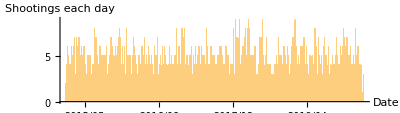

```mathematica
Show[%62,PlotLabel->None,LabelStyle->{20,GrayLevel[0]}]
```

```mathematica
Export["D:\\HOMEWORK\\FOR_HOMEWORK_2020\\20SP\\VE401\\P2\\data-police-shootings\\q2.png",%63,"PNG"]
```

D:\HOMEWORK\FOR_HOMEWORK_2020\20SP\VE401\P2\data-police-shootings\q2.png

```mathematica
data
```

{{Day: Thu 1 Jan 2015,0},{Day: Fri 2 Jan 2015,2},{Day: Sat 3 Jan 2015,1},{Day: Sun 4 Jan 2015,3},{Day: Mon 5 Jan 2015,1},1816,{Day: Fri 27 Dec 2019,4},{Day: Sat 28 Dec 2019,5},{Day: Sun 29 Dec 2019,5},{Day: Mon 30 Dec 2019,3},{Day: Tue 31 Dec 2019,7}}
 |  |  |  |

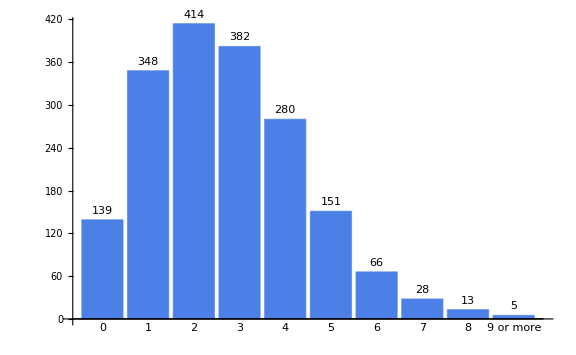

Thread::tdlen: Objects of unequal length in {1600,999} {0.36} cannot be combined.

Set::shape: Lists {System`ConvertersDump`width$275145,System`ConvertersDump`height$275145} and {0.36} {1600,999} are not the same shape.

D:\HOMEWORK\FOR_HOMEWORK_2020\20SP\VE401\P2\data-police-shootings\q31.png

```mathematica
b = BarChart[{139,348,414,382,280,151,66,28,13,5}, ChartLabels->Placed[{0,1,2,3,4,5,6,7,8, "9 or more"}, Below], ImageSize->Large, ChartStyle->RGBColor[77/255, 128/255, 230/255],LabelingFunction->Above]
Export["D:\\HOMEWORK\\FOR_HOMEWORK_2020\\20SP\\VE401\\P2\\data-police-shootings\\q31.png",b,"PNG", ImageResolution->{200}]
```

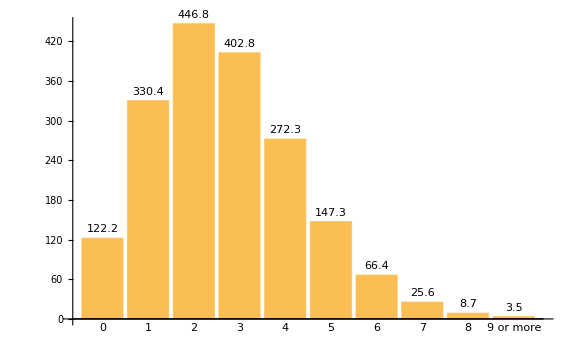

Thread::tdlen: Objects of unequal length in {2400,1499} {0.24} cannot be combined.

Set::shape: Lists {System`ConvertersDump`width$265046,System`ConvertersDump`height$265046} and {0.24} {2400,1499} are not the same shape.

D:\HOMEWORK\FOR_HOMEWORK_2020\20SP\VE401\P2\data-police-shootings\q32.png

```mathematica
c= BarChart[{122.2,330.4,446.8,402.8,272.3,147.3,66.4,25.6,8.7,3.5}, ChartLabels->Placed[{0,1,2,3,4,5,6,7,8, "9 or more"}, Below], ImageSize->Large,LabelingFunction->Above]
Export["D:\\HOMEWORK\\FOR_HOMEWORK_2020\\20SP\\VE401\\P2\\data-police-shootings\\q32.png",c,"PNG", ImageResolution->{300}]
```

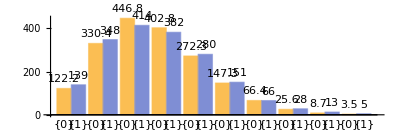

```mathematica
BarChart[Transpose[{{122.2,330.4,446.8,402.8,272.3,147.3,66.4,25.6,8.7,3.5}, {139,348,414,382,280,151,66,28,13,5}}], ChartLabels->Placed[{{0},{1},{2},{3},{4},{5},{6},{7},{8}, {"9 or more"}}, Below], ImageSize->Full, ChartStyle->{RGBColor[77/255, 128/255, 230/255], Automatic}, AspectRatio->1/3, LabelingFunction->Above, BarSpacing->None ]
```

```mathematica
x = {{122.2,330.4,446.8,402.8,272.3,147.3,66.4,25.6,8.7,3.5}, {139,348,414,382,280,151,66,28,13,5}};
Transpose[x]
```

{{122.2,139},{330.4,348},{446.8,414},{402.8,382},{272.3,280},{147.3,151},{66.4,66},{25.6,28},{8.7,13},{3.5,5}}